```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Rank of university*)
r={1,2,3,4,4,6,7,7,9,9,11,12,12,14,15,16,16,18,18,20,21,21,23,23,23,26,27,27,27,30,31,31,31,31,31,36,36,38,38,40,40,40,40,44,44,46,46,48,48,48,51,51,51,54,54,56,56,56,56,56,61,61,61,61,65,65,65,68,68,68,68,72,72,74,74,76,76,76,76,76,76,82,82,82,82,82,87,87,87,87,87,87,93,93,93,93,93,98,98,98,98,102,102,104,104,104,104,104,109,109,111,111,111,111,111,111,111,111,111,120,120,122,122,122,122,122,122,128,129,129,129,129,129,134,134,134,134,134,134,140,140,140,140,140,140,140,140,148,148,148,151,151,151,151,151,151,151,158,158,160,160,160,160,164,164,164,167,167,167,170,170,170,170,174,174,174,174,178,178}; 
(*Citations per publications*)
cpp={24.3,26.3,21.1,22.6,19.2,12,16,17.9,14.4,14.9,23.5,15.5,12,17.7,18.3,18.4,21,18.2,19.1,25.4,19.5,20.9,15.4,13.8,11.5,20.4,13.7,12.9,15.9,15.8,18,12.7,17.2,12.3,22.1,12.5,14.3,14.8,12.6,11.9,12.5,11,12.3,13.8,13.2,13.5,12.1,18.7,2.1,19.9,11.8,17.4,20.6,15.9,9.8,12,12.5,4.5,15.6,10.2,10.9,12.7,12.8,14.9,12.9,10.8,14.3,10.1,14.6,19.5,6.1,8.7,12.4,12.7,10.6,24,13.9,12.7,14.4,7.5,12.3,12.1,12.4,15.3,18.4,18.2,9.9,12,13.2,9,6.4,10.5,11.4,9.8,10.5,15.7,11.1,12.8,12.9,16.3,10,16.9,11.2,10.3,10,14.1,13.4,13.5,16.6,16.4,12.8,7.8,2.3,12.1,10.7,9.6,4.8,13,10.6,9.6,12.4,13.2,11.4,9.7,10.7,12.7,12,11.2,19.4,14.9,12.9,10.3,10.3,6.3,9.1,9.7,10,14.2,14.8,5.4,16.1,5.9,12.1,12.7,12.8,8.4,12.9,8.3,13.8,11.1,9.6,9,1.4,13.3,9.1,4.3,12.1,1.9,7.6,5.1,6.9,12,8.5,8.2,7.7,10.5,9.7,11.7,7.1,1.5,10.2,7.3,4.7,3.2,9.8,9.6,7.8,8.4,3.3,1.8,12,5.2,0.7,5.6,1.1,5.2,7.5,8.4,4.3,6.8,4.1,1.8,4.9,2.7,5.2,1.2,3.8,3.4};
(*Field Weighted Citation Impact*)
fw={2.33,2.34,2.01,2.11,1.82,1.3,1.97,1.64,1.53,1.52,2.05,1.65,1.29,1.93,1.93,1.68,1.98,1.81,1.7,2.25,2.07,2.17,1.53,1.39,1.42,1.72,1.43,1.46,1.61,1.57,1.85,1.42,1.64,1.41,2.11,1.34,1.41,1.67,1.38,1.27,1.57,1.26,1.41,1.42,1.43,1.38,1.32,1.6,0.25,1.96,1.33,1.62,1.89,1.63,1.25,1.45,1.18,0.43,1.48,1.17,1.26,1.54,1.46,1.43,1.44,1.22,1.73,1.16,1.46,1.92,0.65,1.02,1.43,1.25,1.49,1.89,1.35,1.72,1.81,0.89,1.38,1.35,1.36,1.57,1.67,1.41,1.48,1.59,1.54,1.44,0.72,1.2,1.45,1.63,1.25,1.55,1.38,1.43,1.55,1.5,1.24,1.5,1.36,1.19,1.25,1.48,1.5,1.38,1.49,1.69,1.38,0.98,0.31,1.33,1.31,1.15,0.7,1.31,1.41,1.61,1.41,1.53,1.26,1.42,1.14,1.26,1.27,1.2,1.66,1.67,1.26,1.22,1.21,0.56,1.29,1.02,1.06,1.46,1.52,0.8,1.81,0.57,1.23,1.56,1.41,0.77,1.42,0.99,1.43,1.29,1.26,1.12,0.23,1.13,0.85,0.55,1.39,0.29,0.75,0.67,0.72,1.37,1.01,1.11,0.89,0.95,1.17,1.21,0.7,0.3,1.18,0.72,0.55,0.3,1.19,1.19,1.04,1.39,0.53,0.18,1.13,0.75,0.09,0.59,0.25,0.81,0.62,0.8,0.53,0.95,0.5,0.21,0.57,0.32,0.63,0.15,0.43,0.52};
(*Publications Cited in Top 5% of Journals*)
pc1={39.10/100,37.70/100,34.00/100,37.80/100,32.30/100,25.90/100,28.00/100,30.60/100,26.90/100,26.70/100,31.70/100,30.90/100,21.70/100,30.20/100,33.20/100,39.30/100,34.80/100,35.90/100,27.80/100,42.40/100,35.00/100,34.20/100,30.80/100,27.60/100,23.60/100,34.40/100,24.80/100,22.30/100,23.80/100,27.70/100,26.40/100,26.00/100,28.70/100,24.00/100,31.50/100,22.70/100,23.80/100,24.80/100,21.70/100,22.00/100,24.70/100,19.20/100,24.30/100,23.60/100,26.00/100,27.40/100,23.10/100,22.60/100,4.90/100,31.20/100,22.50/100,28.40/100,33.00/100,28.30/100,11.80/100,21.90/100,26.20/100,8.30/100,27.50/100,20.30/100,23.30/100,21.70/100,24.50/100,20.00/100,20.90/100,21.40/100,27.80/100,20.70/100,27.80/100,28.10/100,10.50/100,11.60/100,22.80/100,21.50/100,20.50/100,32.80/100,23.00/100,26.60/100,24.50/100,15.40/100,21.40/100,22.10/100,22.90/100,30.10/100,28.90/100,28.80/100,19.90/100,18.70/100,22.90/100,19.50/100,11.80/100,20.90/100,19.40/100,13.90/100,18.30/100,24.50/100,20.80/100,22.30/100,22.40/100,28.20/100,19.20/100,23.10/100,18.60/100,21.90/100,22.50/100,19.90/100,20.50/100,22.10/100,26.60/100,30.30/100,21.30/100,13.00/100,3.50/100,19.60/100,25.80/100,16.70/100,13.10/100,20.30/100,19.80/100,18.10/100,18.00/100,27.00/100,12.60/100,17.10/100,17.70/100,15.10/100,21.90/100,18.10/100,16.10/100,18.90/100,18.10/100,24.90/100,20.90/100,12.00/100,15.10/100,18.80/100,19.40/100,21.20/100,21.80/100,10.90/100,27.20/100,12.60/100,16.20/100,22.20/100,29.70/100,13.40/100,19.30/100,18.00/100,15.60/100,17.80/100,15.80/100,16.30/100,3.00/100,19.70/100,14.80/100,6.20/100,21.50/100,3.70/100,9.90/100,10.40/100,13.20/100,24.20/100,17.90/100,12.40/100,13.50/100,9.30/100,17.50/100,18.90/100,9.10/100,3.40/100,18.20/100,15.20/100,7.90/100,5.10/100,22.00/100,21.40/100,13.10/100,12.40/100,5.90/100,2.60/100,18.60/100,8.80/100,0.20/100,8.00/100,2.60/100,8.40/100,12.70/100,11.00/100,10.40/100,10.70/100,5.80/100,3.50/100,15.20/100,4.90/100,7.00/100,1.40/100,4.70/100,5.90/100};
(*Publications Cited in Top 25% of Journals*)
pc2={80.10/100,80.20/100,75.10/100,80.70/100,73.70/100,70.30/100,69.90/100,74.50/100,73.60/100,73.50/100,75.20/100,74.80/100,70.20/100,73.20/100,71.10/100,80.90/100,78.70/100,77.50/100,70.90/100,82.20/100,80.10/100,76.20/100,75.30/100,74.80/100,68.60/100,78.80/100,68.80/100,68.50/100,73.30/100,74.60/100,72.60/100,69.50/100,72.60/100,69.90/100,81.00/100,71.80/100,75.80/100,69.90/100,69.30/100,67.60/100,63.50/100,64.00/100,60.00/100,74.40/100,71.10/100,69.60/100,66.30/100,68.00/100,15.60/100,74.60/100,66.60/100,72.00/100,76.20/100,75.20/100,52.50/100,62.80/100,74.50/100,25.30/100,71.40/100,68.30/100,70.20/100,67.40/100,68.00/100,65.60/100,65.40/100,63.30/100,72.00/100,64.60/100,73.60/100,72.50/100,34.70/100,52.50/100,65.20/100,67.80/100,63.70/100,73.80/100,67.00/100,66.50/100,67.40/100,44.60/100,69.00/100,74.00/100,70.40/100,72.70/100,76.90/100,75.00/100,62.30/100,65.80/100,69.90/100,63.20/100,47.20/100,63.20/100,67.50/100,59.30/100,66.50/100,69.40/100,63.00/100,68.40/100,64.60/100,69.00/100,61.40/100,64.00/100,60.30/100,62.60/100,62.40/100,63.30/100,61.40/100,68.00/100,72.60/100,72.40/100,63.70/100,37.60/100,14.50/100,64.50/100,72.20/100,65.20/100,43.60/100,72.10/100,62.20/100,71.00/100,66.60/100,69.80/100,54.30/100,62.10/100,71.50/100,64.10/100,67.70/100,63.40/100,65.50/100,62.40/100,45.50/100,68.20/100,62.30/100,40.80/100,56.80/100,65.00/100,60.90/100,67.70/100,75.90/100,31.50/100,71.90/100,30.90/100,51.60/100,64.80/100,74.20/100,33.90/100,66.50/100,55.80/100,68.40/100,67.10/100,56.90/100,56.80/100,12.70/100,69.40/100,51.70/100,29.40/100,64.80/100,17.80/100,36.60/100,40.80/100,43.40/100,62.20/100,52.40/100,61.20/100,46.50/100,42.00/100,53.40/100,65.20/100,33.90/100,13.00/100,61.50/100,43.60/100,34.30/100,17.90/100,69.20/100,64.40/100,51.70/100,48.00/100,21.90/100,13.10/100,65.10/100,33.50/100,3.30/100,33.00/100,15.60/100,40.70/100,30.40/100,45.70/100,35.20/100,40.10/100,22.30/100,14.70/100,32.80/100,16.50/100,26.00/100,8.90/100,24.20/100,23.70/100};
(*Total publications (current)*)
tp={15431,13651,7100,4558,13511,13737,8056,8733,11605,12321,7715,6546,12709,8918,1241,6584,4283,5101,6126,5024,5971,6316,5198,5829,5847,5309,8319,6831,9345,4483,3337,7900,5554,6721,4873,5204,10806,5285,5454,5162,3010,2872,3534,3399,4344,6691,6807,3055,251,3541,6460,2331,5445,1734,999,3513,3207,363,4166,3985,1806,5193,3844,1210,3697,2813,3518,4070,2120,2759,609,1037,4134,2403,3391,2251,2292,2459,1652,739,2076,2095,3107,2584,2633,2488,2004,1836,2165,2792,771,1887,1775,2263,2395,1637,2554,2422,1430,1754,1798,1531,1600,1621,2073,1378,924,2619,1172,1430,1380,626,391,1736,1301,1613,689,1365,1332,1506,1908,1985,945,952,1378,1693,1671,2228,1393,1081,647,1295,936,558,1160,1393,956,2158,2463,500,1573,461,792,2356,1059,451,1677,904,1061,1485,1357,898,219,1891,815,436,1807,269,621,606,664,864,770,1213,773,693,868,1078,588,251,1307,628,495,251,1140,943,817,798,418,209,1013,600,77,550,254,708,396,657,533,772,405,261,475,340,418,166,390,401};
(*Research expenditures (in millions)*)
re1=10^-6*{433.00,261.00,251.00,137.00,397.00,384.00,320.00,430.00,300.00,298.00,256.00,177.00,445.00,256.00,118.00,181.00,105.00,166.00,242.00,65.00,81.00,204.00,167.00,180.00,178.00,95.00,228.00,187.00,166.00,115.00,150.00,138.00,116.00,158.00,54.00,118.00,123.00,122.00,95.00,112.00,59.00,138.00,85.00,84.00,130.00,147.00,111.00,50.00,127.00,44.00,95.00,79.00,89.00,38.00,221.00,88.00,107.00,56.00,103.00,107.00,32.00,63.00,67.00,77.00,59.00,63.00,52.00,68.00,40.00,20.00,212.00,62.00,50.00,61.00,53.00,30.00,49.00,74.00,47.00,51.00,51.00,30.00,46.00,62.00,38.00,36.00,66.00,21.00,37.00,64.00,79.00,44.00,47.00,52.00,56.00,40.00,47.00,44.00,29.00,46.00,36.00,20.00,47.00,30.00,43.00,25.00,29.00,43.00,30.00,22.00,26.00,23.00,33.00,35.00,14.00,24.00,52.00,38.00,40.00,41.00,29.00,18.00,38.00,19.00,24.00,25.00,29.00,8.00,20.00,20.00,15.00,9.00,12.00,28.00,15.00,16.00,16.00,23.00,21.00,14.00,11.00,30.00,21.00,17.00,13.00,10.00,25.00,18.00,13.00,18.00,23.00,13.00,12.00,13.00,16.00,14.00,13.00,23.00,13.00,7.00,14.00,7.00,10.00,6.00,15.00,9.00,9.00,6.00,9.00,8.00,11.00,8.00,7.00,9.00,1.00,5.00,5.00,7.00,7.00,4.00,8.00,3.00,5.00,5.00,1,3.00,2.00,3.00,3.00,1.00,6.00,3.00,17.00,5.00,2.00,1.00,3.00,3.00};
(*Research expenditures per faculty member (in thousands)*)
re2=10^-3*{1098.98,895.07,966.65,1256.28,677.94,929.04,971.64,1309.79,682.26,724.48,1093.95,845.66,1008.32,1123.70,618.15,905.25,796.15,792.23,910.62,735.02,469.49,704.92,1052.86,1116.79,894.18,663.62,612.22,672.54,603.99,770.04,962.58,328.78,480.32,403.08,543.10,681.33,439.85,620.39,624.48,452.71,760.71,1472.94,739.38,577.64,815.46,443.62,328.72,523.51,866.72,425.90,512.27,412.60,469.87,408.34,2831.83,504.62,746.30,469.51,511.94,498.73,540.15,257.39,386.65,482.10,333.18,365.65,395.30,281.40,423.73,335.37,3474.05,750.86,308.81,290.94,324.20,238.12,321.70,690.20,375.87,299.98,482.58,269.13,338.28,354.22,269.71,284.86,397.91,258.54,334.95,402.09,1008.62,467.25,350.09,456.81,341.76,322.41,385.51,301.78,323.66,244.50,259.86,217.64,397.53,293.09,367.18,174.54,298.08,259.51,297.40,392.79,246.08,244.82,338.69,258.42,173.59,192.92,783.45,539.67,403.99,695.67,334.94,184.27,417.54,521.37,222.31,272.57,249.95,210.34,208.24,337.50,397.99,170.60,333.93,201.04,266.56,233.72,340.17,240.58,1.00,282.77,159.69,1067.21,335.53,127.84,189.26,894.21,173.60,294.57,240.65,191.99,218.82,174.31,1.00,145.40,224.73,313.57,123.24,299.07,249.46,153.87,143.98,98.27,187.12,123.89,247.64,172.95,127.22,97.36,219.28,245.27,120.75,150.94,143.63,132.72,11.45,66.34,69.82,99.82,202.45,180.10,1.00,48.00,219.97,122.37,7.12,40.28,1.00,62.71,50.30,30.22,89.93,107.81,1.00,133.72,81.63,39.14,98.12,56.96};
(*Peer assessment score*)
pa={4.9,4.8,4.7,4.7,4.6,4.4,4.4,4.3,4.6,4.6,3.8,4.3,3.9,4,3.9,4,3.8,3.8,3.8,3.6,4.1,3.7,3.8,3.6,3.7,3.7,3.4,3.7,4,3.5,3.1,3.7,3.4,3.8,3.5,3.5,3.7,3.3,3.4,3.3,3.1,2.7,3.4,3.3,3.1,3.4,3.3,3.2,3.2,3.2,3.1,3,2.9,3.3,2.3,2.9,2.7,3.3,3,3,3,3.1,2.9,2.8,3.1,3.1,2.8,3,2.9,3,2.1,2.8,2.7,2.9,2.6,3,2.6,2.4,2.4,2.7,2.8,2.9,2.8,2.5,2.6,2.7,2.5,2.7,2.6,2.4,2.4,2.5,2.4,2.2,2.5,2.5,2.5,2.5,2.5,2.7,2.7,2.6,2.3,2.6,2.3,2.5,2.4,2.4,2.5,2.2,2.3,2.4,2.8,2.4,2.7,2.3,2.2,2.3,2.3,2,2.2,2.5,2.2,2.3,2.5,2.4,2.2,2.4,2.5,2.1,2.1,2.4,2.2,2.4,2.1,2.2,2.1,1.9,2.1,2.4,2.3,2,2.1,2.2,2.2,1.7,2.3,2.2,1.9,2.2,2.1,2.1,2,2.1,2.2,2,2.3,2.3,2.2,2.3,2.1,2.2,2.3,2.1,2,2,2.2,2.3,2.1,2,2,2.2,2.1,2,2.4,2.1,2.3,1.9,2.1,2,2.2,1.9,1.8,1.7,1.8,1.7,2,2,2.1,1.9,1.8,1.9,2.2,1.8,1.9,1.7,1.7,1.8};
(*Recruiter Assessment Score*)
ra={4.7,4.7,4.5,4.6,4.5,4.2,4.5,4.1,4.3,4.3,4,4.2,4,4.1,4,3.9,4,3.9,3.8,4,4.2,3.9,3.9,3.6,3.7,3.9,3.6,3.8,3.9,3.6,3.5,3.8,3.6,4,3.8,3.8,3.7,3.7,3.6,3.6,3.3,3.2,3.7,3.6,3.3,3.3,3.7,3.7,3.3,3.7,3.8,3.6,3.3,3.7,3,3.4,3.2,4,3.1,3.1,3.8,3.5,3.2,3.4,3.4,3.3,3.2,3.4,3.6,3.6,2.6,3.6,3.3,3.1,3.1,3.4,3.4,2.8,2.8,3.1,3.2,3.5,3.3,3.1,2.8,2.9,2.9,3.3,3.4,3.2,2.8,2.9,3,2.6,2.9,2.9,2.8,2.8,3,2.8,3.6,2.9,3.3,3.1,2.6,3.3,2.8,3,2.7,2.5,3.2,3.5,3.6,3,3.3,3.1,2.6,2.9,2.6,2.7,2.6,3.2,2.5,2.5,3.1,2.5,2.8,3.1,2.9,2.6,2.6,3.1,2.6,2.9,2.9,2.6,2.8,2.5,2.5,3.1,2.8,2.2,2.1,2.6,2.8,2.1,2.6,2.5,2.4,2.8,2.5,2.9,2.7,2.6,2.5,2.5,2.7,3.1,2.8,3,2.8,2.9,2.6,2.8,2.3,2.4,2.5,2.8,2.5,2.5,2.3,2.9,2.5,2.6,3.1,2.9,3.1,2.3,2.6,2.5,3.2,2.3,1.9,2,2.5,2.4,2.7,2.5,2.8,2.4,2.4,2.2,2.6,1.8,2.4,2.1,1.9,2.4};
(*Doctoral degrees granted*)
dg={368,320,279,98,400,382,238,246,317,316,225,177,318,168,185,144,98,156,189,61,114,182,118,132,168,118,208,183,151,92,117,193,149,239,62,128,157,131,134,150,57,92,90,87,98,174,169,59,111,74,127,76,106,47,26,110,57,97,100,109,23,126,92,76,104,104,89,108,35,29,26,31,124,81,97,41,44,61,52,114,48,50,78,61,85,79,73,90,51,76,26,51,58,64,54,59,69,60,41,52,50,39,50,45,38,62,40,54,38,28,44,14,6,33,34,59,11,14,20,4,38,38,46,19,40,33,50,18,27,26,8,23,10,53,25,21,12,28,29,11,31,1,32,38,26,9,45,15,24,20,37,18,11,48,28,20,48,33,13,9,16,33,10,24,15,18,22,34,13,10,21,9,7,21,7,22,16,21,4,3,20,8,3,15,4,15,1,2,6,11,4,15,0,15,12,3,4,6};
(*Acceptance rate (master's and doctoral programs)*)
ar={8.90/100,10.40/100,21.20/100,6.00/100,23.70/100,21.00/100,19.30/100,18.30/100,27.70/100,29.10/100,28.30/100,24.60/100,29.20/100,31.50/100,23.90/100,25.90/100,20.10/100,21.80/100,25.50/100,6.50/100,10.10/100,32.40/100,29.10/100,39.60/100,39.00/100,22.00/100,26.90/100,38.30/100,27.20/100,16.70/100,38.60/100,30.90/100,26.00/100,63.70/100,13.10/100,29.90/100,37.40/100,37.30/100,28.00/100,16.30/100,40.90/100,29.00/100,36.90/100,22.60/100,34.70/100,60.20/100,40.20/100,21.70/100,38.60/100,44.10/100,65.60/100,35.40/100,53.70/100,26.70/100,44.20/100,46.00/100,30.70/100,36.80/100,50.20/100,44.40/100,18.30/100,16.20/100,35.10/100,34.40/100,33.60/100,40.70/100,29.90/100,34.40/100,42.60/100,8.20/100,40.00/100,47.50/100,53.40/100,21.80/100,40.30/100,50.20/100,19.40/100,54.20/100,29.70/100,36.40/100,47.20/100,37.20/100,58.40/100,44.70/100,43.30/100,28.60/100,67.60/100,69.50/100,54.80/100,73.80/100,43.30/100,44.20/100,42.40/100,27.80/100,41.90/100,51.10/100,40.20/100,27.30/100,23.90/100,49.40/100,60.60/100,36.30/100,76.30/100,52.60/100,30.40/100,31.30/100,42.30/100,63.10/100,55.40/100,29.30/100,68.30/100,32.00/100,46.70/100,52.20/100,30.40/100,46.50/100,55.00/100,72.00/100,61.10/100,73.80/100,59.20/100,76.90/100,72.20/100,55.70/100,65.50/100,54.90/100,71.60/100,18.80/100,86.80/100,52.20/100,46.30/100,57.50/100,40.60/100,73.00/100,42.90/100,43.10/100,26.00/100,54.90/100,93.00/100,50.00/100,74.40/100,45.30/100,35.40/100,43.90/100,58.40/100,65.70/100,86.10/100,56.30/100,43.30/100,83.00/100,84.20/100,45.50/100,36.70/100,49.40/100,41.80/100,41.20/100,58.60/100,97.80/100,60.20/100,33.20/100,61.10/100,79.40/100,58.00/100,37.40/100,73.30/100,55.00/100,66.10/100,73.40/100,72.10/100,88.90/100,50.30/100,62.80/100,23.20/100,52.50/100,46.60/100,44.60/100,68.90/100,46.90/100,73.70/100,23.20/100,65.10/100,55.70/100,55.20/100,65.70/100,46.90/100,92.00/100,53.70/100,40.40/100,58.30/100,61.10/100,79.80/100,58.40/100,61.90/100,60.50/100,62.10/100,81.70/100,45.30/100,84.90/100};
(*% of full-time tenured or tenure-track faculty who are elected members of the National Academy of Engineering*)
pt={13.20/100,14.40/100,13.30/100,21.00/100,3.40/100,5.30/100,8.90/100,5.80/100,5.10/100,4.00/100,11.00/100,11.90/100,6.90/100,3.90/100,18.10/100,8.00/100,9.60/100,6.50/100,6.00/100,14.60/100,8.30/100,3.70/100,4.90/100,6.50/100,6.60/100,6.60/100,4.10/100,2.80/100,0.60/100,9.90/100,3.80/100,1.40/100,3.30/100,1.30/100,4.40/100,1.70/100,2.60/100,1.40/100,2.50/100,0,15.20/100,3.00/100,0.90/100,0.70/100,0.70/100,1.40/100,0.90/100,1.00/100,5.50/100,0,1.40/100,1.50/100,1.60/100,5.30/100,0,0,1.30/100,3.00/100,0.50/100,0.50/100,3.30/100,0.40/100,0.60/100,0.60/100,2.20/100,2.20/100,0.70/100,0,3.30/100,0,0,0,1.20/100,1.00/100,1.80/100,0.80/100,0,0,0.80/100,5.20/100,1.90/100,0.90/100,0,0,0,1.60/100,0,0,0,1.20/100,0,0,0.70/100,0,0,4.10/100,0,0,0,1.10/100,0,3.00/100,0,0,0,0,0,0.60/100,0,1.50/100,0,0,0,0,1.30/100,2.30/100,0,1.40/100,0,0,1.20/100,2.10/100,0,0,0,1.20/100,0,0,0,0,0,5.10/100,2.50/100,0,0,0,0,0,0,4.20/100,0,0,0,0,1.40/100,0,0.60/100,0,0,0,0,0,0,0,0,2.10/100,0,0,0,0,0,0,0,0,1.50/100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
(*Doctoral student/faculty ratio*)
dpf={5.9,6.7,5.8,5.1,4.4,6.3,4.5,4.9,5.7,4.5,6.1,6.6,3.7,5.6,5.5,5.6,6.7,4.4,4.1,5.4,4.3,3.8,4.5,6.5,5.5,5.1,3.4,3.8,3.4,3.7,4.7,3.9,3.9,3.2,4.8,4.1,3.6,4.6,4.9,3.3,5.2,4.1,4.7,4.3,3.8,2.6,3,4.2,4.5,5.5,2.9,3.7,3.2,3,1.2,2.6,2.4,3.6,2.6,3.7,3.7,2.8,4.1,3.3,2,2.5,3.6,2.4,2.7,3.8,0.6,2.7,3.4,2.4,3.4,2.6,1.4,1.8,3.2,3.4,2,2.7,2.9,1.5,3.7,2.4,2.6,6.2,3.1,2.3,1.3,3.8,2.5,3.4,1.8,2.8,2.5,2.4,2.7,2,1.8,2.3,1.9,1.3,2.3,2.7,3.1,1.8,1.4,3.4,3.2,1.4,0.9,1.6,2.6,2.9,1.5,1.5,1.9,1,2.2,2.2,1.4,2.4,2.3,2,1.9,2.8,1.7,1.4,2.4,2.2,2.6,2.4,1.5,1.9,0.8,2.8,1.7,1.2,2.6,0.2,1.3,1.3,1.2,5.3,1.6,1.9,2.1,1.6,1.2,1.6,1.3,1.8,1.1,2.8,1.8,1.1,1,1.8,0.6,1.4,1,1.6,1.4,1.3,1.4,2.1,1,3.9,1.2,1,1.5,1.8,0.8,0.7,1.5,1.2,1.8,0.6,1.6,1.9,1,1,0,1.7,1.3,0.9,0.6,1.2,0.3,2.9,0,2.2,2.1,0.6,0.5,0.2};
(*Overall score*)
s={100,96,91,89,89,88,86,86,85,85,84,82,82,80,79,78,78,77,77,76,75,75,74,74,74,72,71,71,71,70,68,68,68,68,68,67,67,66,66,64,64,64,64,63,63,62,62,61,61,61,60,60,60,59,59,58,58,58,58,58,57,57,57,57,56,56,56,55,55,55,55,54,54,53,53,52,52,52,52,52,52,51,51,51,51,51,50,50,50,50,50,50,49,49,49,49,49,48,48,48,48,47,47,46,46,46,46,46,45,45,44,44,44,44,44,44,44,44,44,43,43,42,42,42,42,42,42,41,40,40,40,40,40,39,39,39,39,39,39,38,38,38,38,38,38,38,38,37,37,37,36,36,36,36,36,36,36,35,35,33,33,33,33,32,32,32,31,31,31,30,30,30,30,29,29,29,29,27,27,25,24,21,23,20,0,16,22,22,20,15,20,20,20,23,23,7,17,19};
```

```mathematica
(*The list of variables are*)
{r,cpp,fw,pc1,pc2,tp,re1,re2,pa,ra,dg,ar,pt,dpf,s};
(*normalizing all the variables*)
Nre1=Log[re1*10^6]/Total[Log[re1*10^6]];(*The reason for choosing log for re1 and re2 is :-Graphics-*)
Nre2=Log[re2*10^3]/Total[Log[re2*10^3]];
Ntp= tp/Total[tp];
Ncpp=cpp/Total[cpp];
Nfw=fw/Total[fw];
Npc1=pc1;
Npc2=pc2;
Npa = pa/5;(*I suspect the max is 5*)
Nra = ra/5;(*I suspect the max is 5*)
Ndg = dg/Total[dg];
Nar=ar;
Npt=pt;
Ndpf=dpf/Total[dpf];
Mre1=Log[re1*10^6]/Max[Log[re1*10^6]];
Mre2=Log[re2*10^3]/Max[Log[re2*10^3]];
Mtp= tp/Max[tp];
Mcpp=cpp/Max[cpp];
Mfw=fw/Max[fw];
Mpc1=pc1;
Mpc2=pc2;
Mpa = pa/5;
Mra = ra/5;
Mdg = dg/Max[dg];
Mar=ar;
Mpt=pt;
Mdpf=dpf/Max[dpf];
```

```mathematica
(*Specifying the weights*)
wre1=0.3;
wre2=0.2;
wpa=0.125;
wra=0.125;
wdg=0.09;
war=0.05;
wpt=0.05;
wdpf=0.04;
wre1+wre2+wpa+wra+wdg+war+wpt+wdpf
```

0.98

```mathematica
(*Matching solutions*)
Nf[wfw_,wpc1_,wpc2_,wtp_]:=(0.02-wfw-wpc1-wpc2-wtp)*Ncpp+wfw*Nfw+wpc1*Npc1+wpc2*Npc2+wtp*Ntp+wre1*Nre1+wre2*Nre2+wpa*Npa+wra*Nra+wdg*Ndg+war*Nar+wpt*Npt+wdpf*Ndpf
Mf[wfw_,wpc1_,wpc2_,wtp_]:=(0.02-wfw-wpc1-wpc2-wtp)*Mcpp+wfw*Mfw+wpc1*Mpc1+wpc2*Mpc2+wtp*Mtp+wre1*Mre1+wre2*Mre2+wpa*Mpa+wra*Mra+wdg*Mdg+war*Mar+wpt*Mpt+wdpf*Mdpf
Mixf[wfw_,wpc1_,wpc2_,wtp_]:=(0.02-wfw-wpc1-wpc2-wtp)*Mcpp+wfw*Mfw+wpc1*Mpc1+wpc2*Mpc2+wtp*Mtp+wre1*Nre1+wre2*Nre2+wpa*Mpa+wra*Mra+wdg*Mdg+war*ar+wpt*pt+wdpf*Mdpf(*We are Mixing the normalizations*)
f[wfw_,wpc1_,wpc2_,wtp_,Scdg_]:=(0.02-wfw-wpc1-wpc2-wtp)*Mcpp+wfw*Mfw+wpc1*Mpc1+wpc2*Mpc2+wtp*Mtp+wre1*Nre1+wre2*Nre2+wpa*Mpa+wra*Mra+wdg*dg/Scdg+war*ar+wpt*pt+wdpf*Mdpf(*We are Mixing the normalizations*)
```

```mathematica
index=Range[1,Length[s]];
(*Manipulate[ListPlot[{s/100,f[wfw,wpc1,wpc2,wtp]/Max[f[wfw,wpc1,wpc2,wtp]]},PlotLegends->{"score","test-score","scaled"},ImageSize->Large],{wfw,0,0.02},{wpc1,0,0.02-wfw},{wpc2,0,0.02-wfw-wpc1},{wtp,0,0.02-wfw-wpc1-wpc2}]*)(*Dont Here we have used the fact that re1 and re2 are in the range of 10^6 and 10^3. These will completely determine the shape of the curve. changing weights wont make much difference. *)
(*Manipulate[ListPlot[{s/100,Nf[wfw,wpc1,wpc2,wtp]/Max[Nf[wfw,wpc1,wpc2,wtp]]},PlotLegends->{"score","test-Norm score","scaled"},ImageSize->Large],{wfw,0,0.02},{wpc1,0,0.02-wfw},{wpc2,0,0.02-wfw-wpc1},{wtp,0,0.02-wfw-wpc1-wpc2}]*)(*We are diving by the max so that the max gets set to 1. This is what the article says was done. Check image below.
-Graphics-.*)
(*Manipulate[ListPlot[{s/100,Mf[wfw,wpc1,wpc2,wtp]/Max[Mf[wfw,wpc1,wpc2,wtp]]},PlotLegends->{"score","test-MaxNormscore","scaled"},ImageSize->Large],{wfw,0,0.02},{wpc1,0,0.02-wfw},{wpc2,0,0.02-wfw-wpc1},{wtp,0,0.02-wfw-wpc1-wpc2}]*)(*This is more authentic, since we are scaling everything from 0 to 1 usnig the max scaling, thats how they described some of the factors. The others were percentages*)
Manipulate[ListPlot[{s/100,Mixf[wfw,wpc1,wpc2,wtp]/Max[Mixf[wfw,wpc1,wpc2,wtp]],ExactFormulae},PlotLegends->{"score","test-Mixed Norm score","ExactFormulae"},ImageSize->Large],{wfw,0,0.02},{wpc1,0,0.02-wfw},{wpc2,0,0.02-wfw-wpc1},{{wtp,0.02},0,0.02-wfw-wpc1-wpc2}]
(*This is the correct formulae. HEre we are using the log of the research expenditures and normalizing by diving by the total. All the other variables are scaled to vary between (0,1). Dividing by the maximum for most of them seem to be the right formulae. The best match seems to be achieved when we set wtp=0.2 as the weighting parameter.*)
```

```mathematica
Manipulate[ListPlot[{s/100,f[wfw,wpc1,wpc2,wtp,Scdg]/Max[f[wfw,wpc1,wpc2,wtp,Scdg]],ExactFormulae2},PlotLegends->{"score","test-Ano score","ExactFormulae"},ImageSize->Large],{wfw,0,0.02},{wpc1,0,0.02-wfw},{wpc2,0,0.02-wfw-wpc1},{{wtp,0.02},0,0.02-wfw-wpc1-wpc2},{Scdg,1,500}]
```

```mathematica
(*The exact formuale seems to be*)
ExactFormulae:=Mixf[0,0,0,0.02]/Max[Mixf[0,0,0,0.02]]
ExactFormulae2:=f[0,0,0,0.02,500]/Max[f[0,0,0,0.02,500]]
```

```mathematica
(*This is varying the other parameters a little bit*)
Vf[w1_,w2_,w3_,w4_,w5_,w6_,w7_,w8_,w9_,w10_,w11_,w12_]:=(0.02-w1-w2-w3-w4)*Mcpp+w1*Mfw+w2*Mpc1+w3*Mpc2+w4*Mtp+w5*Mre1+w6*Mre2+w7*Mpa+w8*Mra+w9*Mdg+w10*Mar+w11*Mpt+w12*Mdpf
```

```mathematica
Δw=0.2 (*width of initial region guess. I took the guess around their specified values*)
NMinimize[{Norm[100*(Vf[u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12]/Max[Vf[u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12]])-s],0<=u1<0.02,0<=u2<0.02,0<=u3<0.02,0<=u4<0.02,Max[0,wre1-Δw]<=u5<=Min[wre1+Δw,1],Max[0,wre2-Δw]<=u6<=Min[wre2+Δw,1],Max[wpa-Δw,0]<=u7<=Min[wpa+Δw,1],Max[wra-Δw,0]<=u8<=Min[wra+Δw,1],Max[wdg-Δw,0]<=u9<=Min[wdg+Δw,1],Max[war-Δw,0]<=u10<=Min[war+Δw,1],Max[wpt-Δw,0]<=u11<=Min[wpt+Δw,1],Max[wdpf-Δw,0]<=u12<=Min[wdpf+Δw,1],u1+u2+u3+u4+u5+u6+u7+u8+u9+u10+u11+u12==1},{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12}]
Ans=NArgMin[{Norm[100*(Vf[u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12]/Max[Vf[u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12]])-s],0<=u1<0.02,0<=u2<0.02,0<=u3<0.02,0<=u4<0.02,Max[0,wre1-Δw]<=u5<=Min[wre1+Δw,1],Max[0,wre2-Δw]<=u6<=Min[wre2+Δw,1],Max[wpa-Δw,0]<=u7<=Min[wpa+Δw,1],Max[wra-Δw,0]<=u8<=Min[wra+Δw,1],Max[wdg-Δw,0]<=u9<=Min[wdg+Δw,1],Max[war-Δw,0]<=u10<=Min[war+Δw,1],Max[wpt-Δw,0]<=u11<=Min[wpt+Δw,1],Max[wdpf-Δw,0]<=u12<=Min[wdpf+Δw,1],u1+u2+u3+u4+u5+u6+u7+u8+u9+u10+u11+u12==1},{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12}]
(*(Vf[Ans[[2]][[1]],Ans[[2]][[2]],Ans[[2]][[3]],Ans[[2]][[4]],Ans[[2]][[5]],Ans[[2]][[6]],Ans[[2]][[7]],Ans[[2]][[8]],Ans[[2]][[9]],Ans[[2]][[10]],Ans[[2]][[11]],Ans[[2]][[12]]]/Max[Vf[Ans[[2]][[1]],Ans[[2]][[2]],Ans[[2]][[3]],Ans[[2]][[4]],Ans[[2]][[5]],Ans[[2]][[6]],Ans[[2]][[7]],Ans[[2]][[8]],Ans[[2]][[9]],Ans[[2]][[10]],Ans[[2]][[11]],Ans[[2]][[12]]]])*100*)
```

0.2

{39.321,{u1→0.002175,u2→1.71608×10^-10,u3→2.10359×10^-10,u4→1.55363×10^-10,u5→0.304389,u6→0.0128439,u7→0.220454,u8→0.007958,u9→0.0957346,u10→4.49893×10^-11,u11→0.25,u12→0.106445}}

{0.002175,1.71608×10^-10,2.10359×10^-10,1.55363×10^-10,0.304389,0.0128439,0.220454,0.007958,0.0957346,4.49893×10^-11,0.25,0.106445}

```mathematica
VEF=(Vf[Ans[[1]],Ans[[2]],Ans[[3]],Ans[[4]],Ans[[5]],Ans[[6]],Ans[[7]],Ans[[8]],Ans[[9]],Ans[[10]],Ans[[11]],Ans[[12]]]*100)/Max[Vf[Ans[[1]],Ans[[2]],Ans[[3]],Ans[[4]],Ans[[5]],Ans[[6]],Ans[[7]],Ans[[8]],Ans[[9]],Ans[[10]],Ans[[11]],Ans[[12]]]]
```

{100.,96.8336,92.0025,83.7367,91.7977,93.7177,86.0291,87.5432,90.1406,87.2919,85.3176,84.8572,84.9619,80.8614,80.1114,79.1474,76.095,74.828,77.586,70.0436,71.0727,74.5103,73.1528,77.3614,76.727,71.0845,72.8146,72.8672,71.5611,68.1019,68.6455,70.794,67.6626,72.2416,63.3488,67.25,68.8807,67.5504,67.3232,64.0657,64.8622,62.8851,64.3388,62.7701,63.7219,66.2424,64.25,58.3147,66.4393,60.4139,60.8371,59.6107,60.0223,55.3657,54.6349,57.5445,56.0807,58.8623,59.248,61.5233,52.1802,57.5185,58.4818,56.9328,55.3837,56.6259,55.3471,55.6516,51.6234,49.1566,51.5473,52.2398,55.1248,54.0469,54.1043,50.2215,47.5799,50.4282,50.3905,55.6966,50.8637,49.102,52.3198,49.3726,52.2203,50.0788,51.9134,53.7816,49.4512,50.9865,48.138,51.13,48.8216,49.999,48.6054,50.4536,49.4515,48.6445,46.0528,49.6332,46.8079,44.5495,46.5976,43.812,46.194,45.7766,46.254,46.7618,43.7393,44.3349,45.2816,39.9927,42.8613,44.0407,42.1925,44.9772,43.9974,43.8658,44.4344,40.5955,43.4666,42.4729,43.3456,40.5678,43.6735,43.0277,42.7613,36.3766,41.6261,38.3319,37.7797,37.5921,37.9213,44.1907,36.1026,37.7237,34.755,40.8632,38.1221,37.3496,38.2439,36.3653,38.2244,37.6131,35.8639,38.4816,41.7749,38.1999,35.5437,37.9937,38.5416,35.0488,31.2523,36.6724,36.1906,37.7279,37.7288,38.749,34.1141,31.9158,33.1135,31.8433,32.9047,30.0676,35.1904,31.4848,32.8728,32.8224,31.0234,35.0539,32.5783,30.7348,29.9249,31.8753,17.733,26.9964,29.4777,28.9085,30.4152,23.4982,31.812,23.954,24.4328,24.6253,11.4613,22.6075,19.9254,22.6623,22.364,15.5833,24.4706,26.0125,31.9587,27.3591,21.98,12.3571,19.7032,19.6868}

```mathematica
Manipulate[ListPlot[{s,100*Vf[w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,w11,w12]/Max[Vf[w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,w11,w12]],VEF,ExactFormulae*100},PlotLegends->{"score","test-Vary score","VaryExactFormulae", "ExactFormulae"},ImageSize->Large],{w1,0,0.02},{w2,0,0.02-w1},{w3,0,0.02-w1-w2},{{w4,0.02},0,0.02-w1-w2-w3},{{w5,wre1},0,1-w1-w2-w3-w4},{{w6,wre2},0,1-w1-w2-w3-w4-w5},{{w7,wpa},0,1-w1-w2-w3-w4-w5-w6},{{w8,wra},0,1-w1-w2-w3-w4-w5-w6-w7},{{w9,wdg},0,1-w1-w2-w3-w4-w5-w6-w7-w8},{{w10,war},0,1-w1-w2-w3-w4-w5-w6-w7-w8-w9},{{w11,wpt},0,1-w1-w2-w3-w4-w5-w6-w7-w8-w9-w10},{{w12,wdpf},0,1-w1-w2-w3-w4-w5-w6-w7-w8-w9-w10-w11}]
```

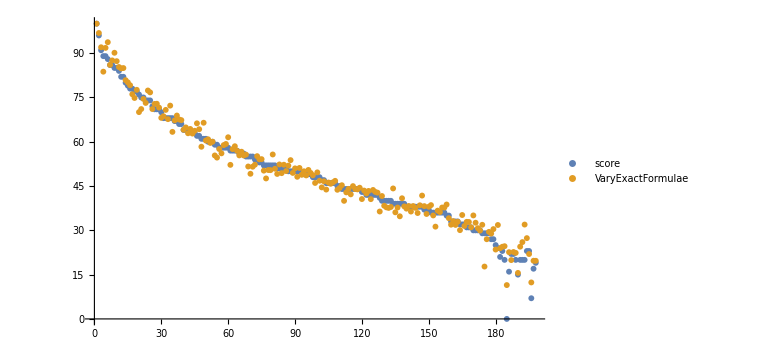

```mathematica
ListPlot[{s,VEF},PlotLegends->{"score","VaryExactFormulae", "ExactFormulae"},ImageSize->Large]
```